# Theoretical Ecology and Evolution: EEMB 595TE Fall 2018

## Day 5

### Lotka-Volterra model for predator and prey with different functional response

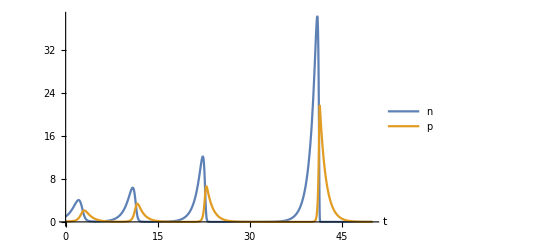

```mathematica
(*parameters*)
r=1;β=2;δ=1;γ=.5;tmax=50;n0=1;p0=.1;h=.05;
(*functional response*)
f[n_]:=(β n)/(1+β n h);
(*differential equations*)
eqs=
{
n'[t]==r n[t] - f[n[t]]p[t],
p'[t]==-δ p[t]+γ f[n[t]] p[t]
};
(*initial conditions*)
inis=
{
n[0]==n0,
p[0]==p0
};
(*state variables*)
vars={n,p};
(*solve the system of differential equations numerically*)
sol=NDSolve[
(*differential equations and initial conditions*)
Join[eqs,inis],
(*state variables*)
vars,
(*time span*)
{t,0,tmax}
];
(*plot simulation*)
Plot[
(*population densities*)
{
n[t]/.sol,
p[t]/.sol
},
(*time span*)
{t,0,tmax},
(*style*)
PlotLegends->{"n","p"},
AxesLabel->{"t"},
AxesOrigin->{0,0},
PlotRange->Full
]
```

### Interactive version and plots in n-p plane

```mathematica
(*lotka-volterra predatory prey with different functional responses*)
DynamicModule[{holling=1,includek=False,showfuncres=False,showtimeplot=True,showphaseplane=True},
Dynamic@Manipulate[
(*protected definitions*)
Module[{system,n,p,sol,t,maxn,maxp,f,equilibrium},
(*functional response*)
f[n_]:=Piecewise[{{β n, holling==1}, {(β n)/(1+β h n), holling==2}, {(α n^2)/(1+α h n^2), holling==3}}];
(*the system of equations*)
system[n_,p_]:=
{
r n Piecewise[{{(1-n/k), includek==True}, {1, True}}] -  f[n]p,
-δ p + γ f[n] p 
};
(*the numerical solution for the system*)
sol=NDSolve[
{
n'[t]==system[n[t],p[t]][[1]],
p'[t]==system[n[t],p[t]][[2]],
n[0]==n0,
p[0]==p0
},
{n,p},
{t,0,tmax}];
(*output*)
Column[{
If[showfuncres,Plot[f[n],
{n,0,nmax},
AxesOrigin->{0,0},
PlotLabel->"functional response",
AxesLabel->{"n","f(n)"}
]],

(*equilibrium for plotrange*)
equilibrium=NSolve[{system[n,p][[1]]==0,system[n,p][[2]]==0,n>0,p>0},{n,p}];

(*time plot*)
If[showtimeplot,Plot[Evaluate[
{n[t],p[t]}/.sol
]
,{t,0,tmax},
AxesOrigin->{0,0},
PlotLabel->"time plot",
AxesLabel->{"t",""},
PlotLegends->{"n(t)","p(t)"},
PlotRange->Full

]],
(*phase plot*)
(*max range for n and p*)
maxn=Max[{1.2n0,3n/.equilibrium}];
maxp=Max[{1.2p0,3p/.equilibrium}];
(*for the locator at the initial population sizes*)
If[showphaseplane, LocatorPane[ 
Dynamic[{n0,p0}],Show[{
(*isoclines*)
ContourPlot[
{
system[n,p][[1]]/n==0,
system[n,p][[2]]/p==0
},
{n,.0001,1.1maxn},{p,.0001,1.1maxp},
PlotRangePadding->None,
PlotLabel->"phase plot and isoclines",
PlotLegends->{"dn/dt=0","dp/dt=0"},
FrameLabel->{"n","p"}
],
(*plot the numerical solution in the phase plot*)
ParametricPlot[{n[t],p[t]}/.sol,{t,0,tmax},
PlotStyle->Darker[Blue],
PlotLegends->"n(t),p(t)"

],
(*arrows showing the direction of the dynamics in the phaseplot*)
VectorPlot[system[n,p],{n,0,1.1maxn},{p,0,1.1maxp},
VectorScale->{Scaled[.05],Scaled[1],None},
VectorStyle->Black
]
}
],
ContinuousAction->False
]]}]
]
,
(*model description*)
Column[
{"Lotka-Volterra predator-prey model with different functional responses",
If[includek,"dn/dt = r n(1 - n/k) - f(n)p","dn/dt = r n - f(n)p"],
"dN/dt= -δ P + γ f(n)P",
Row[{"f(n)=",PopupMenu[Dynamic[holling],{1->"β n",2->"(β n)/(1 + β n h)",3->"(α SuperscriptBox[n, 2])/(1 + α SuperscriptBox[n, 2] h)"}]}],
Row[{"carrying capacity for prey ",Checkbox[Dynamic[includek]]}],

Row[{"show f(n) ",Checkbox[Dynamic[showfuncres]]}],
Row[{"show time plot  ",Checkbox[Dynamic[showtimeplot]]}],
Row[{"show phase-plane  ",Checkbox[Dynamic[showphaseplane]]}]

}
],
(*controllers*)
{{β,2,"β"},0,2,If[holling≤ 2,ContinuousAction->True,ControlType->None]},
{{α,1.2,"α"},0,2,If[holling==3,ContinuousAction->True,ControlType->None](*If[holling==3,Slider,None]*)},
{{h,.1,"h"},0,2,If[holling≥ 2,ContinuousAction->True,ControlType->None]},
{{r,1,"r"},0,2},
{{k,2,"k"},0.01,5,If[includek,ContinuousAction->True,ControlType->None]},
{{γ,1,"γ"},0,2},
{{δ,1,"δ"},0,2},
{{tmax,3,"time end"},.001,50},
{{nmax,3,"plotrange n"},.001,20},
{{n0,.7,"n(0)"},0,2},
{{p0,.4,"p(0)"},0,2},
ControlPlacement->Left]]
```